# Physics through Computational Thinking

## Visual Thinking

1.  learn various ways of visually representing data, information or functions
2. apply skills of visual thinking to represent and solve a few maths and physics problems
3. apply skills of visual thinking to interpret results from graphs

## What is Visual Thinking

Visual thinking is ability to represent and interpret data or any other information through a visual medium such as a data chart, a graph, a picture, mind maps or relationship maps, flow charts etc.

Visual thinking is a way to organize your thoughts and your ability to think and communicate. An image or a graphic is thousand words.

In this course we will learn a lot of visual thinking through computer and also some off the computer as we go along.

## Plotting a graph

Lets start out by learning how to plot a simple function, such as a linear function.

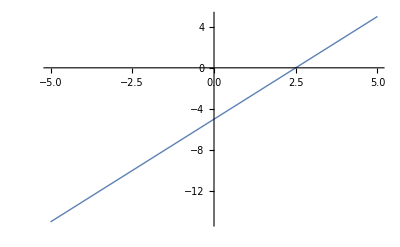

```mathematica
Plot[2x-5,{x,-5,5},PlotStyle->Thick]
```

Plot a polynomial

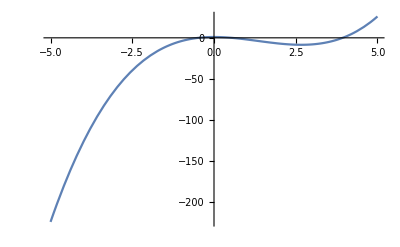

```mathematica
Plot[x^(3)-4x^2+1,{x,-5,5}]
```

Plot a quadratic function

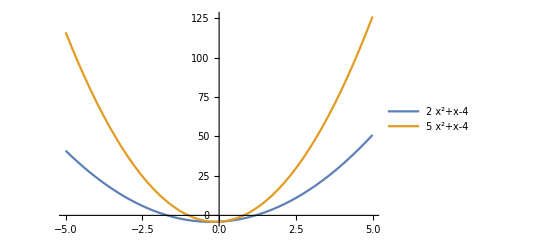

```mathematica
Plot[{2 x^2+x-4,5 x^2+x-4},{x,-5,5},PlotLegends->"Expressions"]
```

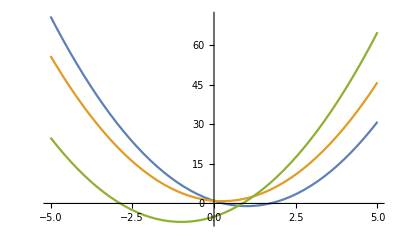

```mathematica
Plot[{2 x^2-4x+1,2 x^2-x+1,2 x^2+4x-5},{x,-5,5}]
```

Plot the most simple quadratic function

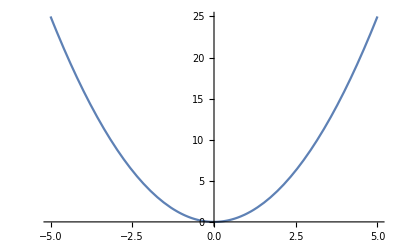

```mathematica
Plot[x^2,{x,-5,5}]
```

## Understanding Quadratic Function

Lets vary the parameters of a general quadratic function using Manipulate construct and see what is the effect of each parameter on the function.

a x^2+b x+c=0

Manipulate[Plot[a x^2+b x+c,{x,-5,5},PlotRange→{{-5,5},{Automatic,10}}],{{a,1},-2,2},{{b,0},-5,5},{{c,0},-1,1}]

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-5,5},PlotRange->{{-5,5},{-10,10}},Frame->True],{{a,1},-5,5},{{b,0},-5,5},{{c,0},-5,5}]
```

## Quadratic function & Quadratic-like behaviour

Quadratic functions are of great importance in physics as quadratic potentials are associated with simple harmonic oscillator which has a simple sinusoidal oscillatory motion.

Thus it is often of great importance to identify regions or domains where other functions behave like a harmonic oscillator potential or quadratic potential.

Lets consider the following functions

f_1(x)=-cos(x)
f_2(x)=-(sin(x))/x
f_3(x)=-1/x+1/x^2       for x > 0

Exercise: Plot these functions and identify if these functions have quadratic behaviour at their minima and maxima?

## Function behaviour near x=0

Exercise:  Can you plot √x, x, x^2, x^3, x^4 etc. for x>0 on the same plot/graph on paper. Keep in mind how they differ near x=0.

## Radicals and Logarithms

Exercise 1:  Plot x,√x and log(x). Do they intersect at any point? Plot them and find out how they behave at small x and large x?

Exercise 2:  Plot x^(1/3) and log(x). Do they intersect at any point?

Exercise 3:  Visually find the solution of the transcendental equation x^(1/n)=log(x).  For what values of n there are solutions to this equation. When do you have exactly one solution?

```mathematica
Plot[{x^(1/3),Log[x]},{x,0,10},Frame->True,PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{x^(1/n),Log[x]},{x,0,100},Frame->True,PlotLegends->{x^(1/"n"),Log[x]}],{{n,2},1,5}]
```

Solution 3: We can also solve this analytically. Let’s say that exactly one solution happens for n=n_0 and (say) at x=x_0. Then, for n=n_0 and x=x_0 we have both the functions evaluate to the same value and their derivatives also evaluate to the same value, thus

x_0^(1/n_0)=log(x_0)

((and,         (ⅆ x^(1/n_0))/ⅆx|)_(x=x_0)=(ⅆ log(x))/ⅆx|)_(x=x_0)

last equation simplifies to

1/n_0 x_0^(1/n_0)/x_0=1/x_0 |        ⇒    | x_0^(1/n_0)=n_0 |      ⇒       | log(x_0)=n_0 log(n_0)

Substituting in the first equation we get

n_0=n_0 log(n_0) |     ⇒      log(n_0)=1 |     ⇒     | n_0=ⅇ

Solving for x_0 we get

log(x_0)=n_0 log(n_0) |     ⇒      log(x_0)=ⅇ |     ⇒     | x_0=ⅇ^ⅇ

Numerically

```mathematica
N[E]
```

2.71828

```mathematica
N[E^E]
```

15.1543

## Exercises

1. Explore numerical function N[x].

(a) N calculates numerical value of any expression. Lets find out Pi and E (the Euler number e) to 10 digits by evaluating the following commands.

```mathematica
N[Pi]
```

```mathematica
N[Pi,10]
```

```mathematica
N[E,10]
```

(b) Find Pi to 100 digits.

(c) Find 2^(1/2) and 2^(1/3) up to 16 digits.

2. Can you reproduce the plot below by figuring out the suitable Mathematica code (one line only). Reproduce also the plot styling that is x-range, y-range, labeling, colors, line stroke, frame etc. You may need to look up documentation of the Plot function to be able to do this. Its a good idea to start navigating into documentation and also learn how to make your figures look nicer. See if you can figure out a few styling techniques on your own to make the figure look even better that what is presented here.